```mathematica
Clear[sol,t]
equals={x1''[t]==m2(x2[t]-x1[t])/Norm[{x2[t],y2[t]}-{x1[t],y1[t]}]^3+m3(x3[t]-x1[t])/Norm[{x3[t],y3[t]}-{x1[t],y1[t]}]^3,x2''[t]==m1(x1[t]-x2[t])/Norm[{x1[t],y1[t]}-{x2[t],y2[t]}]^3+m3(x3[t]-x2[t])/Norm[{x3[t],y3[t]}-{x2[t],y2[t]}]^3,x3''[t]==m1(x1[t]-x3[t])/Norm[{x1[t],y1[t]}-{x3[t],y3[t]}]^3+m2(x2[t]-x3[t])/Norm[{x2[t],y2[t]}-{x3[t],y3[t]}]^3,y1''[t]==m2(y2[t]-y1[t])/Norm[{x2[t],y2[t]}-{x1[t],y1[t]}]^3+m3(y3[t]-y1[t])/Norm[{x3[t],y3[t]}-{x1[t],y1[t]}]^3,y2''[t]==m1(y1[t]-y2[t])/Norm[{x1[t],y1[t]}-{x2[t],y2[t]}]^3+m3(y3[t]-y2[t])/Norm[{x3[t],y3[t]}-{x2[t],y2[t]}]^3,y3''[t]==m1(y1[t]-y3[t])/Norm[{x1[t],y1[t]}-{x3[t],y3[t]}]^3+m2(y2[t]-y3[t])/Norm[{x2[t],y2[t]}-{x3[t],y3[t]}]^3};
boundary={x1[0]==x01,y1[0]==y01,x2[0]==x02,y2[0]==y02,x3[0]==x03,y3[0]==y03,x1'[0]==vx01,y1'[0]==vy01,x2'[0]==vx02,y2'[0]==vy02,x3'[0]==vx03,y3'[0]==vy03};
{{"x01",Slider[Dynamic[x01],{-5,5},Appearance->"Labeled"]},{"y01",Slider[Dynamic[y01],{-5,5},Appearance->"Labeled"]},{"x02",Slider[Dynamic[x02],{-5,5},Appearance->"Labeled"]},{"y02",Slider[Dynamic[y02],{-5,5},Appearance->"Labeled"]},{"x03",Slider[Dynamic[x03],{-5,5},Appearance->"Labeled"]},{"y03",Slider[Dynamic[y03],{-5,5},Appearance->"Labeled"]},{"vx01",Slider[Dynamic[vx01],{-1,1},Appearance->"Labeled"]},{"vy01",Slider[Dynamic[vy01],{-1,1},Appearance->"Labeled"]},{"vx02",Slider[Dynamic[vx02],{-1,1},Appearance->"Labeled"]},{"vy02",Slider[Dynamic[vy02],{-1,1},Appearance->"Labeled"]},{"vx03",Slider[Dynamic[vx03],{-1,1},Appearance->"Labeled"]},{"vy03",Slider[Dynamic[vy03],{-1,1},Appearance->"Labeled"]}}

{{"m1",Slider[Dynamic[m1],{0,5},Appearance->"Labeled"]},{"m2",Slider[Dynamic[m2],{0,5},Appearance->"Labeled"]},{"m3",Slider[Dynamic[m3],{0,5},Appearance->"Labeled"]}}
sol=NDSolve[{equals,boundary},{x1,y1,x2,y2,x3,y3},{t,-15,200}]
```

{{x01, | },{y01, | },{x02, | },{y02, | },{x03, | },{y03, | },{vx01, | },{vy01, | },{vx02, | },{vy02, | },{vx03, | },{vy03, | }}

{{m1, | },{m2, | },{m3, | }}

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],x2→InterpolatingFunction[…],y2→InterpolatingFunction[…],x3→InterpolatingFunction[…],y3→InterpolatingFunction[…]}}

```mathematica
Quiet[Animate[Show[ParametricPlot[{Evaluate[{x1[t0],y1[t0]}/.sol]},{t0,t-15,t},PlotStyle->Orange],
ParametricPlot[{Evaluate[{x2[t0],y2[t0]}/.sol]},{t0,t-15,t},PlotStyle->Green],
ParametricPlot[{Evaluate[{x3[t0],y3[t0]}/.sol]},{t0,t-15,t}],Graphics[{PointSize[0.01],Point[{{First[Evaluate[x1[t]/.sol]],First[Evaluate[y1[t]/.sol]]},{First[Evaluate[x2[t]/.sol]],First[Evaluate[y2[t]/.sol]]},{First[Evaluate[x3[t]/.sol]],First[Evaluate[y3[t]/.sol]]}}]}],Axes->False,PlotRange->{{(First[Evaluate[x1[t]/.sol]]+First[Evaluate[x2[t]/.sol]]+First[Evaluate[x3[t]/.sol]])/3-10,(First[Evaluate[x1[t]/.sol]]+First[Evaluate[x2[t]/.sol]]+First[Evaluate[x3[t]/.sol]])/3+10},{(First[Evaluate[y1[t]/.sol]]+First[Evaluate[y2[t]/.sol]]+First[Evaluate[y3[t]/.sol]])/3-10,(First[Evaluate[y1[t]/.sol]]+First[Evaluate[y2[t]/.sol]]+First[Evaluate[y3[t]/.sol]])/3+10}}],{t,0,200,0.01},AnimationRunning->True,AnimationRate->5]]
```

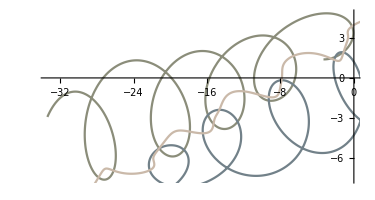

```mathematica
Show[ParametricPlot[{Evaluate[{x1[t],y1[t]}/.sol]},{t,0,200},ColorFunction->"Rainbow"],
ParametricPlot[{Evaluate[{x2[t],y2[t]}/.sol]},{t,0,200},ColorFunction->Hue],
ParametricPlot[{Evaluate[{x3[t],y3[t]}/.sol]},{t,0,200},ColorFunction->"TemperatureMap"]]
```

```mathematica
Manipulate[VectorPlot[{a,b},{x,0,1},{y,0,1},VectorPoints->2],{a,-1,1},{b,-1,1}]
```

```mathematica
ListPlot[Table[{First[Evaluate[x2[t]/.sol]],First[Evaluate[y2[t]/.sol]]},{t,t-10,t,0.1}]
```